# What constrains wildfire burn areas?

## Introduction

The goal of this 3-week project is to identify features of the landscape that tend to constrain burn areas once a wildfire starts. As western North America once again suffers a record-breaking drought, an intense fire season is thought to ensue in the second half of 2021. The only semi-effective response to such fire forecasts is to manage vegetated lands with high amounts of fuel - plant biomass. Managing fuels means reducing the fuel loading to create fire breaks, stripes of barren land to limit the spread of the fire, or pruning lower tree branches to reduce the probability of fire crowning.  We aim to improve these managements strategies by identifying landscape features, natural or artificial, that are effective in limiting fire spread in the goal of emulating them.

The hypothesis of this project is that wildfire burn areas are constrained by different landscape elements such as fuel availability, natural fuel breaks such as water bodies and topography and artificial fuel breaks such as roads and forest clearing. The objectives are to 1) visualize different landscape layers simultaneously with burn areas for a high-level exploration of our hypothesis, 2) define quantitative metrics to relate landscape layers to burn areas, 3) and develop statistical and mechanistic modeling tools to describe  burn area shape and distribution. 

While the analysis in this project applies to wildfires anywhere on Earth, we decided to limit the geographic range to California due to relatively better data accessibility and because of the severe fire season that will follow this year.

## Outline

Data import, data wrangling, and function definitions

Burn perimeter data: data import and wrangling

Burn perimeter data: create California wildfires dataset

Vegetation Classification: data import and wrangling

Elevation: data import and wrangling

Function definitions for visualizing and describing the statistics of vegetation and elevation inside and around fires

Vector data: import roads and rivers overlying and surrounding wildfires

Function definitions for analyzing boundaries in vector form: roads and rivers

Vector boundaries

Raster data: vegetation classification

Machine Learning methods: vegetation classification

Machine Learning methods: vegetation and elevation combined

Future work: testing the wind-driven vs fuel-driven fire paradigms

Future work: weather data

An extensive resource for fire perimeters is the Monitoring Trends in Burn Severity (MTBS) website. On the website, one can download the raw data from the Burned Areas Boundaries Dataset . I downloaded the zip file and put it in the same folder as this notebook. This dataset contains the perimeters of all reported burns, including wildfires and prescribed fires, in the United States from 1984 to 2019. This data will be imported and wrangled in the “Import burn perimeter data: data wrangling” section. The perimeter data will then be subset to only include California wildfires and will be analyzed in “Import burn perimeter data: data analysis” section.

## Data import, data wrangling, and function definitions

### Burn perimeter data: data import and wrangling

Credit for this section: Mads Bahrami’s Wolfram Community post on analyzing MTBS data

#### Import shape file either from the .shp file

Importing the dataset takes a minute.

```mathematica
(*perimeterData=Import[NotebookDirectory[]<>"mtbs_perimeter_data.zip","Data"];*)
```

#### Check out elements of the shape file

```mathematica
(*Import[NotebookDirectory[]<>"mtbs_perimeter_data.zip","Elements"]*)
```

#### It seems from the below that the datum used is the North American 1983 datum.

```mathematica
(*Import[NotebookDirectory[]<>"mtbs_perimeter_data.zip","CoordinateSystemInformation"]*)
```

#### Define projection for plotting on a map

```mathematica
(*proj=ReplacePart[Import[NotebookDirectory[]<>"mtbs_perimeter_data.zip","Projection"]/.("ReferenceModel"->_)->("ReferenceModel"->"NAD831986"),1->"Mercator"]*)
```

#### Extract dimensions of dataset and show the keys of the association

```mathematica
(*perimeterData//Dimensions*)
```

```mathematica
(*perimeterData⟦1⟧//Association//Keys*)
```

There is only one layer in the shapefile

```mathematica
(*Lookup[perimeterData,"LayerName"]*)
```

#### What are the reported properties of each burn?

```mathematica
(*Lookup["Labels"][perimeterData]*)
```

#### There are 26558 burns in the dataset

```mathematica
(*Dimensions[Lookup["Geometry"][perimeterData]]*)
```

#### What is the structure of “LabeledData”

```mathematica
(*Lookup["LabeledData"][perimeterData]⟦1,1⟧*)
```

Essentially, “LabeledData” contains lists giving each fire the information indicated by “Labels”. Our goal is to create a Dataset of each fire to be able to extract any of the information listed in “Labels”. To do this, we need to create for each fire a list of associations with “Labels” as keys and “LabeledData” as values. This is what we do below.

#### Clean up “LabeledData” and create a list of associations

```mathematica
(*assoc=AssociationThread[Lookup["LayerName"]@perimeterData,#]&@(*Create an association between fire name and "LabeledData"*)
Apply[Association,(*For each fire, replace the List Head into an Associtiation*)
Transpose/@Apply[Thread[#1->#2]&,(*Thread (Key->) onto the data of each fire, then transpose*)
MapAt[StringDelete["_"],Lookup["LabeledData"][perimeterData],{1,All,1}](*Remove underscores from all keys*)
,{2}]
,{2}];*)
```

#### Create an association for Geometry that allows us to join it to “assoc”

```mathematica
(*geometry=First/@(*Reduce "useless" dimension of this list of associations*)
(AssociationThread[Lookup["LayerName"]@perimeterData,#]&@(*Define name of each fire and point to corresponding geometry*)
Map[<|"Geometry"->#|>&,Lookup[{"Geometry"}]@perimeterData,{3}](*Create association to join with assoc*));*)
```

#### Combined “assoc” and “geometry” and replace FilledCurve objects by Polygon objects and wrap all Polygon points by GeoGridPosition to represent accurate projection

```mathematica
(*ds=Dataset[Join@@@Transpose[Lookup["mtbs_perims_DD"][{assoc,geometry}]]][All,{"IgDate"->(DateObject[Most[#],"Day"]&),"Geometry"->(ReplaceAll[#,{FilledCurve[{{Line[pnts_]},__}]:>Polygon[GeoGridPosition[pnts,proj]],Polygon[pnts_]:>Polygon[GeoGridPosition[pnts,proj]]}]&)}];*)
```

#### Save as WXF file in case imported ds was just computed

```mathematica
(*BinaryWrite[NotebookDirectory[]<>"perimiterDataset.wxf",ExportByteArray[ds,"WXF"]];*)
```

```mathematica
(*Close[NotebookDirectory[]<>"perimiterDataset.wxf"];*)
```

### Burn perimeter data: create California wildfires dataset

IMPORTANT NOTE: I saved ds as a .wxf file for faster loading and so I didn’t have to repeat the data wrangling process above.

#### Import fire perimeter dataset

This is much faster than doing all of the above

```mathematica
ds=Import[NotebookDirectory[]<>"perimiterDataset.wxf"];
```

#### Check out the structure of “ds” for a random fire

The fires in “ds” are not sorted

```mathematica
ds[2]
```

#### Redefine “proj” in case the first time it was define was commented out

“proj” is the projection definition used in the MTBS Burned Areas Boundaries Dataset. It will be the default projection used for geo-computations in the rest of this notebook.

```mathematica
proj=ReplacePart[Import[NotebookDirectory[]<>"mtbs_perimeter_data.zip","Projection"]/.("ReferenceModel"->_)->("ReferenceModel"->"NAD831986"),1->"Mercator"]
```

{Mercator,ReferenceModel→NAD831986}

#### Filter keeping only CA wildfires that occur after 2000 and ReverseSort according to fire size

This is because the remote sensing data we will be using later is only available after year 2000.

```mathematica
dsCa=Query[ReverseSortBy[#BurnBndAc&]]@Query[Select[StringContainsQ[#["EventID"],"CA"]&&StringContainsQ[#["IncidType"],"Wildfire"]&&#["IgDate"]["Year"]>2000&]][ds];
```

#### Create a dataset where the geometry of each fire is a list of points wrapped in Polygons instead of being wrapped first by GeoGridPosition

This is to make subsequent computations faster

```mathematica
dsCaPoly=dsCa[All,{"Geometry"->(ReplaceAll[#,Polygon[GeoGridPosition[x_,_]]:>Polygon[x]]&)}];
```

#### Save for community post

```mathematica
(*BinaryWrite[NotebookDirectory[]<>"communityPostCaPolyDs.wxf",ExportByteArray[{dsCa,dsCaPoly},"WXF"]];*)
```

```mathematica
(*Close[NotebookDirectory[]<>"communityPostCaPolyDs.wxf"];*)
```

### Vegetation Classification: data import and wrangling

#### Description

Now that we have the burn area perimeters, we can import and analyze vegetation classification data. We will be using the MODerate resolution Imaging Spectroradiometer (MODIS) land cover classification layer based on the University of Maryland (UMD) vegetation classes. The UMD classification is called the “LC_Type2” layers within the MODIS land cover dataset. This is a yearly remote sensing dataset that started in 2001. I have downloaded the appropriate  netCDF (.nc) dataset using the AρρEEARS website for which one needs to create a NASA EARTHDATA login. The details of the request I made for this data download is in the image copied below. It should allow complete reproduction of the import, wrangling, and analysis below.

-Graphics-

The imported data are raster graphics, 1 for each year, where each pixel is assigned 1 of 16 numbers number from 1 to 255. Each number represents a different vegetation class. These 19 imported images have the native MODIS sinusoidal projection. They will each be reprojected using the “proj” projection defined in the  “Burn perimeter data” sections. Then, they will be saved in a .wxf file to be re-imported faster later since re-projection takes a while for such large images.

#### Get land cover file name

```mathematica
landCoverFileName=First@FileNames[__~~"umd.nc",NotebookDirectory[]<>"MODIS\\netcdf"]
```

C:\Users\mrada\Documents\wss\MODIS\netcdf\MCD12Q1.006_500m_aid0001_umd.nc

#### Projection information comes from the User Guide of MODIS Land Cover ellipsoid parameters

As mentioned above, MODIS’ native projection is Sinusoidal with a different reference ellipsoid.

```mathematica
projLandCover={"Sinusoidal","ReferenceModel"->{Quantity[6.371007181*^6, "Meters"],Quantity[6.371007181*^6, "Meters"]}}
```

{Sinusoidal,ReferenceModel→{6.37101×10^6 m,6.37101×10^6 m}}

#### Check out the datasets included in the downloaded .nc file

```mathematica
Import[landCoverFileName,{"Datasets"}]
```

{/time,/ydim,/xdim,/LC_Type2,/crs,/QC}

#### Import the UMD land cover classification data

```mathematica
lc=Import[landCoverFileName,{"Datasets","/LC_Type2"}];
```

#### Check out its dimesions

```mathematica
lc//Dimensions
```

{19,2439,2858}

As mentioned above, there area 19 of these land cover classification maps each for a single year going from 2001 to 2019.

#### UMD vegetation classifications

Each pixel in the land classification image is given a classification number which corresponds to a given vegetation type listed in the User Guide. Below, I create an association linking each number to the corresponding description.

```mathematica
lcPropVals=Sort@DeleteDuplicates@Flatten@lc[[1]]
```

{0,1,2,4,5,6,7,8,9,10,11,12,13,14,15,255}

```mathematica
vegClass=Rule@@@Thread[{lcPropVals,{"Water Bodies","Evergreen Needleleaf Forests","Evergreen Broadleaf Forests","Deciduous Broadleaf Forests","Mixed Forests","Closed Shrublands","Open Shrublands","Woody Savannas","Savannas","Grasslands","Permanent Wetlands","Croplands","Urban and Built-up Lands","Cropland/Natural Vegetation Mosaics","Non-Vegetated Lands","Unclassified"}}]
```

{0→Water Bodies,1→Evergreen Needleleaf Forests,2→Evergreen Broadleaf Forests,4→Deciduous Broadleaf Forests,5→Mixed Forests,6→Closed Shrublands,7→Open Shrublands,8→Woody Savannas,9→Savannas,10→Grasslands,11→Permanent Wetlands,12→Croplands,13→Urban and Built-up Lands,14→Cropland/Natural Vegetation Mosaics,15→Non-Vegetated Lands,255→Unclassified}

#### Define color rule for colorized image

```mathematica
colRule=Rule@@@Thread[{lcPropVals,Join[{Black},Take[ColorData[54,"ColorList"],Length[lcPropVals]-2],{LightBlue}]}]
```

{0→GrayLevel[0],1→RGBColor[0.782803, 0.164904, 0.400458],2→RGBColor[0.909499, 0.613916, 0.204196],4→RGBColor[0.806577, 0.385397, 0.762768],5→RGBColor[0.698817, 0.873304, 0.295247],6→RGBColor[0.378897, 0.873304, 0.787549],7→RGBColor[1, 0.529198, 0.324819],8→RGBColor[1, 0.998367, 0.434775],9→RGBColor[0.873304, 0.150484, 0.255131],10→RGBColor[0.723598, 0.791043, 0.963806],11→RGBColor[0.85037, 0.558389, 0],12→RGBColor[1, 0.998856, 0.00207523],13→RGBColor[0.273106, 0.542992, 0.495583],14→RGBColor[1, 0.740871, 0.828473],15→RGBColor[0.630091, 0.148196, 0.579461],255→RGBColor[0.87, 0.94, 1]}

#### Extract region boundaries for California

This is to compute the output range of the GeoImageProjection, it should be over the state of California. This range will be slightly larger than the range of the data. The GeoImageTransformation function below will be told to fill these background values, where no data is present, with “0”.

```mathematica
calGeoRan=GeoGraphics[GeoRange-> Entity["AdministrativeDivision",{"California","UnitedStates"}],GeoProjection->proj];
targetRange=Values@First@Options[calGeoRan,"PlotRange"]
```

{{-1.39038×10^7,-1.2648×10^7},{3.74875×10^6,5.20292×10^6}}

#### Extract GeoRanges of imported dataset

```mathematica
xList=Import[landCoverFileName,{"Datasets","/xdim"}];
yList=Import[landCoverFileName,{"Datasets","/ydim"}];
```

```mathematica
lcRange={xList[[{1,-1}]],yList[[{-1,1}]]}
```

{{-1.11902×10^7,-9.86648×10^6},{3.56913×10^6,4.69869×10^6}}

#### Apply GeoImageTransformation to change the projection i.e. project the land cover classification image using the default projection

Here, we use the undocumented function GeoGraphics`GeoImageTransformation to process the land cover classification image for each year and re-project it the the default projection specified by variable “proj”. Below is shown a description of this undocumented function.

```mathematica
?GeoGraphics`GeoImageTransformation
```

IMPORTANT NOTE: The projections were precomputed and saved in a file called “lcType2ImageProj.wxf” which is imported below. One can re-process the images by un-commenting the cell right after this “text” cell. Doing this will take several minutes.

```mathematica
(*lcImageProj=AssociationThread[Range[2001,2019],GeoGraphics`GeoImageTransformation[Image[lc⟦#⟧,"Byte",ColorSpace->"Grayscale"],projLandCover->{"Mercator","ReferenceModel"->"NAD831986"},lcRange->targetRange,Background->0]&/@Range[Length[lc]]];*)
```

```mathematica
lcImageProj=Import[NotebookDirectory[]<>"lcType2ImageProj.wxf"];
```

#### In case projection was done in this instance, save as WXF file

```mathematica
(*BinaryWrite[NotebookDirectory[]<>"lcType2ImageProj.wxf",ExportByteArray[lcImageProj,"WXF"]];*)
```

```mathematica
(*Close[NotebookDirectory[]<>"lcType2ImageProj.wxf"];*)
```

#### What is the most abundant vegetation class in CA in 2019?

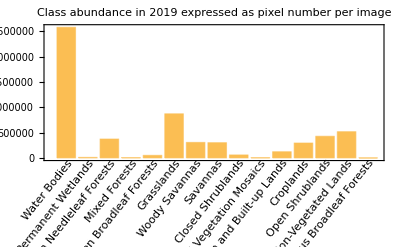

```mathematica
BarChart[KeyDrop[KeyMap[Lookup[vegClass,#]&,Counts@Flatten[ImageData[lcImageProj[2019],"Byte"]]],{Missing["KeyAbsent",0],"Unclassified"}],ChartLabels->Placed[Automatic,{{0.5,0},{0.9,1}},Rotate[#,(2/7) Pi]&],Frame->True,PlotLabel->"Class abundance in 2019 expressed as pixel number per image"]
```

Most of the pixels in the downloaded MODIS land cover classification image are “water bodies” corresponding to pixels of the Pacific Ocean, rivers, and lakes.

### Elevation: data import and wrangling

#### Description

California elevation data was downloaded from the HydroSHEDS website. The elevation data downloaded was the “HydroSHEDS_DEM” file, where DEM stands for Digital Elevation Model, at 15 arc-second resolution for North America from their Dropbox account. The approach is to feed both vegetation and elevation data to the same analysis workflow. Therefore, Images of California elevation will be re-projected to the “proj” variable as was done for the vegetation data.

#### Import elevation data

```mathematica
elevDat=Import[NotebookDirectory[]<>"na_dem_15s_grid.zip",{"ARCGrid","Data"}];
```

#### Explore dataset elements

```mathematica
Import[NotebookDirectory[]<>"na_dem_15s_grid.zip",{"ARCGrid","Elements"}]
```

{Centering,CentralScaleFactor,CoordinateSystem,CoordinateSystemInformation,Data,DataFormat,Datum,ElevationRange,Graphics,GridOrigin,Image,InverseFlattening,LinearUnits,Projection,ProjectionName,RasterSize,ReferenceModel,ReliefImage,SemimajorAxis,SemiminorAxis,SpatialRange,SpatialResolution,StandardParallels}

#### The projection used was Equirectangular according to the technical documentation

```mathematica
projElev="Equirectangular";
```

#### Get dataset size

```mathematica
Import[NotebookDirectory[]<>"na_dem_15s_grid.zip",{"ARCGrid","RasterSize"}]
```

{22320,8400}

#### Get the spatial range of the elevation data

```mathematica
elevRange=QuantityMagnitude@Import[NotebookDirectory[]<>"na_dem_15s_grid.zip",{"ARCGrid","SpatialRange"}]
```

{{25.,60.},{-145.,-52.}}

#### Get the resolution of the elevation data in degrees (of latitude/longitude)

This also matches the one reported in the technical documentation

```mathematica
elevResolution=((First@*Differences/@elevRange)/Dimensions[elevDat])[[1]]
```

0.00416667

#### Get the spatial range of the state of California (with padding) in Equirectangular projection

```mathematica
caRange=Reverse@Values@First@Options[GeoGraphics[GeoRange->Entity["AdministrativeDivision",{"California","UnitedStates"}],GeoProjection->"Equirectangular"],"PlotRange"]
```

{{32.0619,42.4709},{-124.9,-113.619}}

#### Find the subset of the elevation dataset that corresponds to California

```mathematica
takeCA={Round@((elevRange[[1,2]]-Reverse@caRange[[1]])/elevResolution),Round@((caRange[[2]]-elevRange[[2,1]])/elevResolution)}
```

{{4207,6705},{4824,7532}}

#### Take only the pixels of the elevation raster that overlies the state of California (with padding)

```mathematica
elevImCa=ImageTake[Image[Reverse[elevDat],"Bit16",ColorSpace->"Grayscale"],takeCA[[1]],takeCA[[2]]];
```

#### Re-project the elevation raster to “proj” and remove the alpha channel

The alpha channel was removed because none of the raster pixels should be transparent. Note that here we use the undocumented function GeoGraphics`GeoImageTransformation again as we did for the vegetation classification data.

```mathematica
elevImProj=RemoveAlphaChannel[GeoGraphics`GeoImageTransformation[elevImCa,"Equirectangular"->proj,Reverse[caRange]->targetRange]];
```

#### Elevation histogram of the state of California in meters above sea level (ASL)

The high density of values around 0 is due to many pixels overlying the Pacific Ocean.

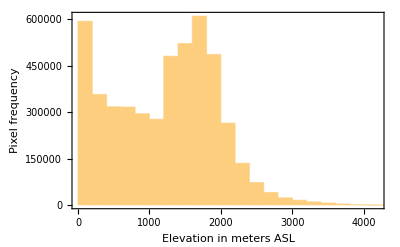

```mathematica
Histogram[Select[Flatten@Reverse[elevDat][[Span@@takeCA[[1]],Span@@takeCA[[2]]]],#>0&],Frame->True,FrameLabel->{"Elevation in meters ASL","Pixel frequency"}]
```

### Function definitions for visualizing and describing the statistics of vegetation and elevation inside and around fires

#### Define function to compute fire bounding box

Returns the bounds of the wildfire polygon in the “Mercartor” projection specified in variable “proj”.

```mathematica
getBoundingBox[burnGeom_]:=With[{normBurnGeom=Normal[burnGeom]},If[Length[normBurnGeom]==1,MinMax/@Transpose[normBurnGeom/.Polygon[x_]:>x],MinMax/@Transpose[Flatten[normBurnGeom/.Polygon[x_]:>x,1]]]]
```

#### Define function to compute the corresponding range in the vegetation classification image

Returns the range of data in the land cover or elevation images that overlay the wildfire polygon bounds from the “getBoundingBox” function.

```mathematica
findRange[fireBoundingBox_,fullRange_,imDimensions_]:=With[{xPosa=(First@Differences@fullRange⟦1⟧)/(imDimensions⟦1⟧-1),xPosb=First@fullRange⟦1⟧-(First@Differences@fullRange⟦1⟧)/(imDimensions⟦1⟧-1),
yPosa=(First@Differences@fullRange⟦2⟧)/(imDimensions⟦2⟧-1),yPosb=First@fullRange⟦2⟧-(First@Differences@fullRange⟦2⟧)/(imDimensions⟦2⟧-1)},{imDimensions⟦2⟧-Reverse[Round[(#-yPosb)/yPosa]&/@Last[fireBoundingBox]],Round[(#-xPosb)/xPosa]&/@First[fireBoundingBox]}]
```

#### Define function that returns the 1) rasterized burn area and 2) the corresponding vegetation classification image as a list. They should have the same size.

The rangePad argument of the “burnAreaRasIm” function is the number of pixels with which to pad the burn raster and the classification or elevation image.

```mathematica
burnAreaRasIm[burnGeom_,imRange_,imFull_,rangePad_:0]:=Module[{im,burnRas,xTakeRange,yTakeRange,fireBoundingBox},
fireBoundingBox=getBoundingBox[burnGeom];
{yTakeRange,xTakeRange}=findRange[fireBoundingBox,imRange,ImageDimensions[imFull]];
im=ImageTake[imFull,yTakeRange+{-1,1}rangePad,xTakeRange+{-1,1}rangePad];
burnRas=Rasterize[Graphics[Style[burnGeom,Antialiasing->False],PlotRange->fireBoundingBox],
RasterSize->{First@Differences@xTakeRange+1,First@Differences@yTakeRange+1}];
burnRas=ImagePad[ColorNegate@burnRas,rangePad];
{burnRas,im}
]
```

#### Define function to visualize vegetation classes inside, around, and outside fires

```mathematica
viz[{burnRas_,im_},colorRule_:None]:=DynamicModule[{colorizedLCImage=Colorize[ImageData[im,"Byte"],ColorRules->colorRule,ColorFunction->Hue]},
Manipulate[
If[StringMatchQ[highlightWhere,"inside"],HighlightImage[colorizedLCImage,burnRas,"Lighten",ImageSize->Medium],
If[StringMatchQ[highlightWhere,"outside"],HighlightImage[colorizedLCImage,ColorNegate@burnRas,"Lighten",ImageSize->Medium],
If[StringMatchQ[highlightWhere,"around"],HighlightImage[colorizedLCImage,Dilation[burnRas,DiskMatrix[5]]-burnRas,"Lighten",ImageSize->Medium]]]],
{highlightWhere,{"inside","around","outside"}}]
]
```

Example for the largest California wildfire, the RANCH fire of 2018:

```mathematica
viz[burnAreaRasIm[dsCaPoly[1,"Geometry"],targetRange,lcImageProj[2018],10],colRule]
```

#### Define function to compute vegetation statistics w.r.t. fire

Returns an association where each element is the number of the burn raster pixels occupied by a given vegetation class. The keys are ReverseSort(ed) according to the number of pixels.

```mathematica
getVegList[vegClassAssociation_,{burnRas_,imLC_},region_]:=If[StringMatchQ[region,"inside"],ReverseSort@KeyMap[Lookup[vegClassAssociation,#]&,Counts@PixelValue[imLC,burnRas,"Byte"]],
If[StringMatchQ[region,"around"],ReverseSort@KeyMap[Lookup[vegClassAssociation,#]&,Counts@PixelValue[imLC,Dilation[burnRas,DiskMatrix[5]]-burnRas,"Byte"]]]]
```

Example for the largest California wildfire, the RANCH fire of 2018:

```mathematica
getVegList[vegClass,burnAreaRasIm[dsCaPoly[1,"Geometry"],targetRange,lcImageProj[2018],10],"inside"]
```

<|Evergreen Needleleaf Forests→5162,Woody Savannas→4854,Grasslands→1359,Closed Shrublands→809,Savannas→695,Open Shrublands→426,Permanent Wetlands→18,Mixed Forests→3,Deciduous Broadleaf Forests→2,Non-Vegetated Lands→1|>

#### Define function to identify dominant vegetation types inside and around fires

This function also returns a dominance number: the ratio of the pixels of the most dominant vegetation types divided by the number of all pixels.

```mathematica
getPrimVegClass=Function[j,{First[Keys[j]],Function[i,N[i[[1]]/Total[i]]]@Values@j}];
```

Example for the largest California wildfire, the RANCH fire of 2018:

```mathematica
getPrimVegClass[getVegList[vegClass,burnAreaRasIm[dsCaPoly[1,"Geometry"],targetRange,lcImageProj[2018],10],#]]&/@{"inside","around"}
```

{{Evergreen Needleleaf Forests,0.387276},{Woody Savannas,0.28502}}

This indicates that the dominant vegetation type inside the RANCH fire was Evergreen Needleleaf Forests and it accounted for ~ 39% of burn area. However, Woody Savannas dominated the area around the fire with ~29% of the area around.

### Vector data: import roads and rivers overlying and surrounding wildfires

#### Load from .wxf file

```mathematica
{roadMapsByType,roadPolyRas,boundaryByType,morphCompNum}=Import[NotebookDirectory[]<>"communityPostVector.wxf"];
```

#### Define thickness of each vector element in the “getRoadMap” function below

```mathematica
thicknesses=<|"road_primary"->0.005,"road_primary_ramp"->0.005,"road_primary_bridge"->0.005,"road_motorway"->0.005,"road_motorway_ramp"->0.005,"road_motorway_bridge"->0.005,"road_secondary"->0.003,"road_secondary_ramp"->0.003,"road_secondary_bridge"->0.003,"road_tertiary"->0.002,"road_tertiary_ramp"->0.002,"road_tertiary_bridge"->0.002,"road_minor"->0.001,"road_trunk"->0.001,"waterway_river"->0.005,"waterway_canal"->0.005|>;
```

#### Function to return a rasterized map of roads and rivers overlying and surrounding fires

```mathematica
getRoadMap[proj_,bounds_,dims_,opts___]:=With[{map=GeoGraphics[opts,PlotRange->bounds,GeoProjection->proj,GeoBackground->"VectorMinimal",GeoZoomLevel->12,Background->Black]},
Rasterize[map/. {
Annotation[{style_,prim_},layer:{"line",lt_,_},type_]:>
If[!KeyExistsQ[thicknesses,lt],Nothing,
Annotation[{Directive[Antialiasing->False,White,Thickness[thicknesses[lt]]],prim},layer,type]],
Annotation[{style_,prim_},layer_,type_]:>Nothing},RasterSize->dims,Background->Black]]
```

Example for the RUSH fire of 2012:

```mathematica
getRoadMap["Mercator",GIS`RangeTransformation[getBoundingBox[dsCaPoly[2,"Geometry"]],proj->"Mercator"],{1000,1000}]
```

-Graphics-

#### Function to return a rasterized map of either roads or rivers

This function will be used  to determine the most effective types of boundaries to wildfires

```mathematica
getRoadMapByType[proj_,bounds_,dims_,types_,opts___]:=With[{map=GeoGraphics[opts,PlotRange->bounds,GeoProjection->proj,GeoBackground->"VectorMinimal",GeoZoomLevel->12,Background->Black]},
Rasterize[map/. {
Annotation[{style_,prim_},layer:{"line",lt_,_},type_]:>
If[!StringMatchQ[lt,types],Nothing,
Annotation[{Directive[Antialiasing->False,White,Thickness[0.001]],prim},layer,type]],
Annotation[{style_,prim_},layer_,type_]:>Nothing},RasterSize->dims,Background->Black]]
```

getType is different from getRoadMapByType in that it is fed a map instead of computing it itself

```mathematica
getType[map_,dims_,types_]:=Rasterize[map/. {
Annotation[{style_,prim_},layer:{"line",lt_,_},type_]:>
If[!StringMatchQ[lt,types],Nothing,
Annotation[{Directive[Antialiasing->False,White,Thickness[0.001]],prim},layer,type]],
Annotation[{style_,prim_},layer_,type_]:>Nothing},RasterSize->dims,Background->Black]
```

Example for the Happy Camp Complex of 2014 for roads:

```mathematica
getRoadMapByType["Mercator",GIS`RangeTransformation[getBoundingBox[dsCaPoly[16,"Geometry"]],proj->"Mercator"],{300,300},___~~"road"~~__]
```

-Graphics-

#### Function to rasterize a polygon of a burn area to Highlight relevant vectors in (colored) road maps

```mathematica
roadRasterize[geom_]:=ColorConvert[Rasterize[Graphics[Style[Normal@geom,Antialiasing->False],PlotRange->getBoundingBox[geom]],
RasterSize->{1000,1000}],"Grayscale"]
```

#### Compute roadMaps, roadMapsColored, and rasterized fire polygons for all California wildfires since 2001

```mathematica
(*roadPolyRas=ResourceFunction["DynamicMap"][roadRasterize[dsCaPoly[#,"Geometry"]]&,Range[Length[dsCaPoly]]];*)
```

```mathematica
(*roadMapsByType2=Table[With[{map=GeoGraphics[PlotRange->GIS`RangeTransformation[getBoundingBox[dsCaPoly[i,"Geometry"]],proj->"Mercator"],GeoProjection->"Mercator",GeoBackground->"VectorMinimal",GeoZoomLevel->12,Background->Black]},{getType[map,{300,300},___~~"road"~~__],getType[map,{300,300},___~~"waterway"~~__]}],{i,Range[201,400]}];*)
```

#### Save road

```mathematica
(*BinaryWrite[NotebookDirectory[]<>"roadMapsByType2.wxf",ExportByteArray[roadMapsByType2,"WXF"]];*)
```

```mathematica
(*Close[NotebookDirectory[]<>"roadMapsByType2.wxf"];*)
```

```mathematica
(*roadMaps=ResourceFunction["DynamicMap"][With[{bbEqui=GIS`RangeTransformation[getBoundingBox[dsCaPoly[#,"Geometry"]],proj->"Mercator"]},ColorConvert[getRoadMap["Mercator",bbEqui,{1000,1000}],"Grayscale"]]&,Range[Length[dsCa]]];*)
```

```mathematica
(*roadMapsColored=ResourceFunction["DynamicMap"][With[{bbEqui=GIS`RangeTransformation[getBoundingBox[dsCaPoly[#,"Geometry"]],proj->"Mercator"]},getRoadMapColored["Mercator",bbEqui,{300,300}]]&,Range[Length[dsCa]]];*)
```

### Function definitions for analyzing boundaries in vector form: roads and rivers

#### Function to get fraction of boundaries bounded by each vector component using the roadMapsByType

```mathematica
boundaryTypes[fireRas_,map_]:=Module[{imDia=Dilation[map,DiskMatrix[0.5]],
fireRasResized=EdgeDetect[ImageResize[fireRas,{300,300}],1],
boundaryLength,boundTypeCounts},
boundaryLength=ImageMeasurements[fireRasResized,"Total"];
boundTypeCounts=ImageMeasurements[Binarize[fireRasResized-ColorSeparate[imDia,"R"],0.5],"Total"];
1-boundTypeCounts/boundaryLength]
```

Compute the boundary types for the largest 400 fires in California since 2000

```mathematica
(*boundaryByType=ResourceFunction["DynamicMap"][{boundaryTypes[roadPolyRas[[#]],roadMapsByType[[#,1]]],boundaryTypes[roadPolyRas[[#]],roadMapsByType[[#,2]]]}&,Range[400]];*)
```

#### Function to calculate the number of morphological components formed by roads or rivers

```mathematica
getMorphCompNum[fireRas_,map_]:=Module[{morphComp=MorphologicalComponents[ImageSubtract[ColorNegate@ImageResize[fireRas,{300,300}],Dilation[map,DiskMatrix[2]]],0.9],selectComps},
selectComps=Select[Tally[Flatten[morphComp]],#[[2]]>100&][[All,1]];
Length[selectComps]-1]
```

Compute the number of morphological components for the largest 400 fires in California since 2000

```mathematica
(*morphCompNum=ResourceFunction["DynamicMap"][{getMorphCompNum[roadPolyRas[[#]],roadMapsByType[[#,1]]],getMorphCompNum[roadPolyRas[[#]],roadMapsByType[[#,2]]]}&,Range[400]];*)
```

#### Function to plot morphological components containing more than 100 pixels

```mathematica
plotMorphComp[fireRas_,map_]:=Module[{morphCompRanch=MorphologicalComponents[ImageSubtract[ColorNegate@ImageResize[fireRas,{300,300}],Dilation[map,DiskMatrix[2]]],0.9],
selectComps},
selectComps=Select[Tally[Flatten[morphCompRanch]],#[[2]]>100&][[All,1]];
Colorize[morphCompRanch/.(x_Integer/;(!MemberQ[selectComps,x])->0),ImageSize->Small]]
```

Example for the Ranch fire of 2012 for roads:

```mathematica
plotMorphComp[roadPolyRas[[1]],roadMapsByType[[1,1]]]
```

-Graphics-

#### Save files necessary for vector analysis in community post

```mathematica
(*BinaryWrite[NotebookDirectory[]<>"communityPostVector.wxf",ExportByteArray[{roadMapsByType,roadPolyRas,boundaryByType,morphCompNum},"WXF"]];*)
```

```mathematica
(*Close[NotebookDirectory[]<>"communityPostVector.wxf"];*)
```

## Vector boundaries

```mathematica
GeoGraphics[{EdgeForm[Black],FaceForm[Red],Tooltip[#3,#1<>", "<>DateString@#2]&@@@Query[;;60,{"IncidName","IgDate","Geometry"}][dsCa]},GeoRange->Entity["AdministrativeDivision",{"California","UnitedStates"}]]
```

-Graphics-

### Variable effectiveness of roads and rivers as barriers

The effectiveness of roads and rivers as barriers to wildfire spread varies from fire to fire. From some of the most intense fires in the presence of wind, the creation and transport of embers by wind can spread a fire across wide fire breaks like roads and rivers. In that case, what one sees is similar to the left panel of the figure below where the Ranch fire spreads across multiple roads, colored in magenta. An equivalent view of the same phenomenon is that these roads divide the fire raster, colored in black, into multiple disconnected components which we will expand upon below. Rivers are not primary features of that landscape as they are sparse and only border 6.1% of the fire in the case of the Ranch fire. From the vector map on the right panel, one can see that water bodies occasionally block fires.

The Ranch fire of 2018: the presence of roads does not guarantee containment

```mathematica
Grid[{{"",Style["Roads",18],Style["Rivers",18],Style["Map",18]},
{Rotate[Style["Boundary %",18],π/2],Style[NumberForm[boundaryByType[[1,1]]*100,2],16],Style[NumberForm[boundaryByType[[1,2]]*100,2],16],""},{Rotate[Style["Maps and rasters",18],π/2],HighlightImage[ImageResize[roadPolyRas[[1]],{300,300}],Thinning[roadMapsByType[[1,1]]],ImageSize->Small,ImagePadding->10],HighlightImage[ImageResize[roadPolyRas[[1]],{300,300}],{Blue,Thinning[roadMapsByType[[1,2]]]},ImageSize->Small,ImagePadding->10],GeoGraphics[dsCa[1,"Geometry"],GeoBackground->"VectorMinimal",GeoZoomLevel->12,ImageSize->Small]}}]
```

| Roads | Rivers | Map
Boundary % | 41. | 6.1 | 
Maps and rasters | -Graphics- | -Graphics- | -Graphics-

Roads are a more effective barrier in the case of the Happy Camp Complex according to the left panel in the figure below. This is due to roads only dividing the complex into 3 regions, indicating that the fire jumped across 2 roads at most only even though roads bordered 47% of the fire, more than the Ranch fire above. An important landscape feature around many fires is that roads and rivers are often co-located as seen by comparing the panels below. This might confound the analysis of the effectiveness of roads versus rivers as fire barriers.

The Happy Camp Complex of 2014: a case where roads and rivers are effective wildfire barriers

```mathematica
Grid[{(*{Style["The Happy Camp Complex of 2014: a case where roads and rivers are effective wildfire barriers",18],SpanFromLeft,SpanFromLeft},*){"",Style["Roads",18],Style["Rivers",18],Style["Map",18]},
{Rotate[Style["Boundary %",18],π/2],Style[NumberForm[boundaryByType[[16,1]]*100,2],16],Style[NumberForm[boundaryByType[[16,2]]*100,2],16],""},{Rotate[Style["Maps and rasters",18],π/2],HighlightImage[ImageResize[roadPolyRas[[16]],{300,300}],Thinning[roadMapsByType[[16,1]]],ImageSize->Small,ImagePadding->10],HighlightImage[ImageResize[roadPolyRas[[16]],{300,300}],{Blue,Thinning[roadMapsByType[[16,2]]]},ImageSize->Small,ImagePadding->10],GeoGraphics[dsCa[16,"Geometry"],GeoBackground->"VectorMinimal",GeoZoomLevel->12,ImageSize->Small]}}]
```

| Roads | Rivers | Map
Boundary % | 47. | 31. | 
Maps and rasters | -Graphics- | -Graphics- | -Graphics-

We can use the idea of splitting fire rasters into morphological components based on road and river vectors to quantify their effectiveness. When fires jump more often across roads, they are split into more morphological components. Thus, a smaller number of components indicates a more effective barrier given a certain boundary percentage. The figure below shows the same two example fires above but split into morphological components based on road vectors. The Ranch fire has 14 morphological components compared to the Happy Camp Complex’s 3. This result quantifies the observation we made above that roads are a more effective barrier to fire spread in case of the latter. This statement is based also on the proportion of the fire boundaries being occupied by roads being similar, 41 and 47%.

Tirtha: Include dNBR with LAI

Roads splitting fire rasters into multiple morphological components: a measure of effectiveness

```mathematica
Grid[{
{"",Style["Ranch fire",18],Style["Happy Camp Complex",18]},
{Rotate[Style["#",18],π/2],Style[morphCompNum[[1,1]],16],Style[morphCompNum[[16,1]],16]},
{Rotate[Style["Morphological components",18],π/2],plotMorphComp[roadPolyRas[[1]],roadMapsByType[[1,1]]],plotMorphComp[roadPolyRas[[16]],roadMapsByType[[16,1]]]}}]
```

| Ranch fire | Happy Camp Complex
# | 14 | 3
Morphological components | -Graphics- | -Graphics-

```mathematica
Rasterize[Grid[{
{plotMorphComp[roadPolyRas[[1]],roadMapsByType[[1,1]]],plotMorphComp[roadPolyRas[[16]],roadMapsByType[[16,1]]]}}]]
```

-Graphics-

### Statistics over the largest 400 fires in California since year 2000

NOTE: I chose only 400 fires because Mathematica was crashing when trying to compute maps for all 864 wildfires

We now perform a statistical analysis of the fire boundaries for the largest 400 fires in California since 2000. In the figure below, we plot the histogram of the proportion of fires bounded by roads in the top-left panel. What we see in this histogram is that a decreasing number of fires has more road boundaries; an expected result. The majority of the fires have close to no roads at the boundary or inside.  On the top-right is the histogram of the number of morphological components formed by the roads. A significant portion are split into 3 or more morphological components, but the majority has less than 5 components. In other words, most fires jump across less than 4 roads. The ListLinePlot at the bottom-left of the figure indicates that it is the largest fires that are the most bounded by roads. But this is not  due to higher road effectiveness as a barrier. In fact, this is due to a higher density of roads overlying the burn area as indicated by the bottom-right figure. In other words, the larger the fire, the more roads it jumps across, and the more of its perimeter is bounded by roads.

Roads: Histograms and ListLinePlots of the proportion of fires bounded by roads and number of morphological components due to roads in relation to fire size

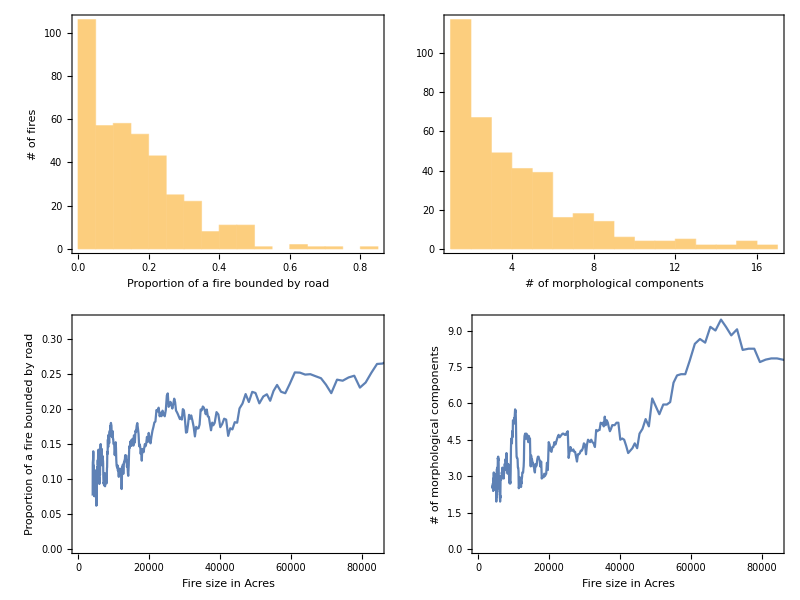

```mathematica
Grid[{{Histogram[boundaryByType[[All,1]],ImageSize->Medium,Frame->True,FrameLabel->{Style["Proportion of a fire bounded by road",14],Style["# of fires",14]}],Histogram[morphCompNum[[All,1]],ImageSize->Medium,Frame->True,FrameLabel->{Style["# of morphological components",14]}]},
{ListLinePlot[MovingAverage[Transpose[{Normal@dsCa[;;400,"BurnBndAc"],boundaryByType[[All,1]]}],20],ImageSize->Medium,Frame->True,FrameLabel->{Style["Fire size in Acres",14],Style["Proportion of a fire bounded by road",14]}],ListLinePlot[MovingAverage[Transpose[{Normal@dsCa[;;400,"BurnBndAc"],morphCompNum[[All,1]]}],20],ImageSize->Medium,Frame->True,FrameLabel->{Style["Fire size in Acres",14],Style["# of morphological components",14]}]}}]
```

A significantly lower proportion of the fires encounter rivers, compared to roads, as boundary as indicated by the histogram on the top-left subfigure below. The smaller proportion and number of morphological components is likely due to rivers being less numerous than roads on the landscape. Moreover, in contrast to roads, the proportion of a fire bounded by a river does not increase with fire size nor does the number of morphological components. The difference in these trends with size between roads and rivers are thought to be due to human-built roads being heterogeneously distributed over a landscape, with higher densities in and around cities. Rivers are more homogeneously distributed over the landscape.

Rivers: Histograms and ListLinePlots of the proportion of fires bounded by rivers and number of morphological components due to rivers in relation to fire size

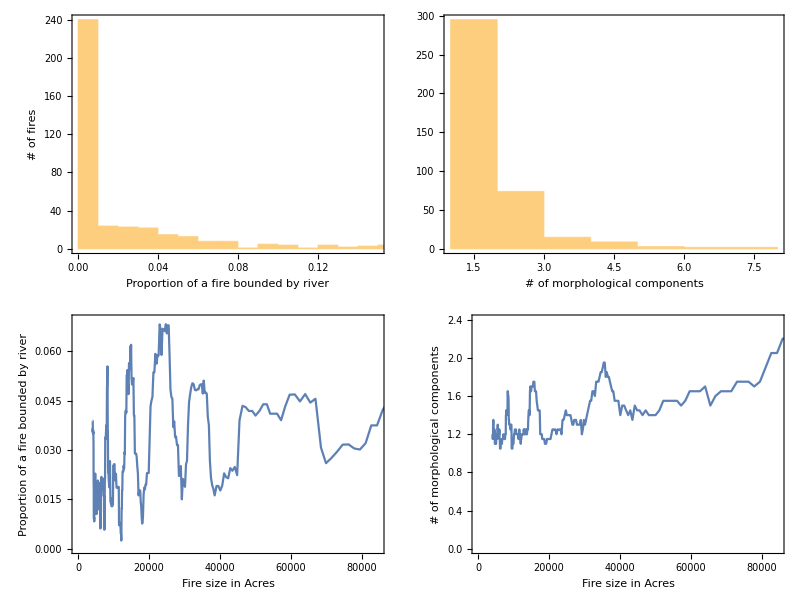

```mathematica
Grid[{{Histogram[boundaryByType[[All,2]],ImageSize->Medium,Frame->True,FrameLabel->{Style["Proportion of a fire bounded by river",14],Style["# of fires",14]}],Histogram[morphCompNum[[All,2]],ImageSize->Medium,Frame->True,FrameLabel->{Style["# of morphological components",14]}]},
{ListLinePlot[MovingAverage[Transpose[{Normal@dsCa[;;400,"BurnBndAc"],boundaryByType[[All,2]]}],20],ImageSize->Medium,Frame->True,FrameLabel->{Style["Fire size in Acres",14],Style["Proportion of a fire bounded by river",14]}],ListLinePlot[MovingAverage[Transpose[{Normal@dsCa[;;400,"BurnBndAc"],morphCompNum[[All,2]]}],20],ImageSize->Medium,Frame->True,FrameLabel->{Style["Fire size in Acres",14],Style["# of morphological components",14]}]}}]
```

By calculating the ratio of the proportion bounded by a road or river and the number of morphological components, we are able to evaluate which of roads or barriers are more effective fire breaks. The figure below shows that number to be around 5% for roads and 2% for rivers. In other words, for every road a fire jumps, another road constrains an additional 5% of its perimeters compared to 2% for rivers. Thus, for the same length of roads and rivers, we expect roads to be more effective in stopping the spread of the fire.

Roads are twice as effective at bounding fires

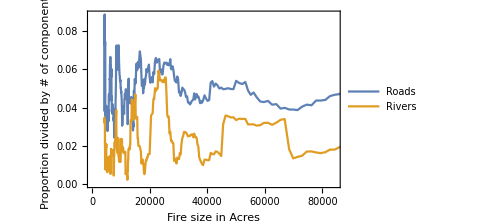

```mathematica
ListLinePlot[MovingAverage[Transpose[{Normal@dsCa[;;400,"BurnBndAc"],boundaryByType[[All,#]]/morphCompNum[[All,#]]}],20]&/@{1,2},ImageSize->Medium,Frame->True,FrameLabel->{Style["Fire size in Acres",14],Style["Proportion divided by # of components",14]},PlotLegends->{"Roads","Rivers"}]
```

## Raster data

### Explore dominant vegetation types inside and around fires

#### Compute dominant vegetation type inside and around the fire

The code below creates an association for each fire where the dominant vegetation type inside and around the fire are reported along with their dominance numbers. The dominance number is the ratio of the number of pixels occupied by the dominant vegetation class divided by the total number of pixels inside the burn area.

```mathematica
(*dominantVegClassAssociation=
With[{bC=burnAreaRasIm[Lookup[#,"Geometry"],targetRange,lcImageProj[Lookup[#,"IgDate"]["Year"]],10]},
(ToExpression[Values[Query[{"BurnBndLat","BurnBndLon","BurnBndAc"}][#]]]->{
"inside"->getPrimVegClass[getVegList[vegClass,bC,"inside"]],
"around"->getPrimVegClass[getVegList[vegClass,bC,"around"]]})
]&/@Normal[dsCaPoly];*)
```

#### Import if already saved

```mathematica
dominantVegClassAssociation=Association[Import[NotebookDirectory[]<>"burnVegClassAssociationType2.wxf"]/.{x_,y_}:>Association[x,y]];
```

Example for Ranch fire of 2012

```mathematica
dominantVegClassAssociation[[;;2]]
```

<|{39.269,-122.775,427048}→<|inside→{Evergreen Needleleaf Forests,0.387276},around→{Woody Savannas,0.28502}|>,{40.603,-120.09,306811}→<|inside→{Grasslands,0.999701},around→{Grasslands,0.991457}|>|>

The Keys for this association are {lat, lon, acres}. These were was used in an earlier version of the notebook to create a classifier for predicting vegetation dominance based on them. But then I opted against them because the good results were probably artefacts of dominant vegetation being a function of topography, location, and elevation inherently.

#### Save burnVegClassAssociation as WXF file

```mathematica
(*BinaryWrite[NotebookDirectory[]<>"burnVegClassAssociationType2.wxf",ExportByteArray[burnVegClassAssociation,"WXF"]];*)
```

```mathematica
(*Close[NotebookDirectory[]<>"burnVegClassAssociationType2.wxf"];*)
```

#### Filter out cases where dominant vegetation is “unclassified”

```mathematica
dominantVegClassAssociationFiltered=Query[Select[StringQ[#inside[[1]]]&&StringQ[#around[[1]]]&&!StringMatchQ[#around[[1]],"Unclassified"]&]]@Association[dominantVegClassAssociation/.{x_,y_}:>Association[x,y]];
```

#### Vegetation bar plot inside and around burn areas

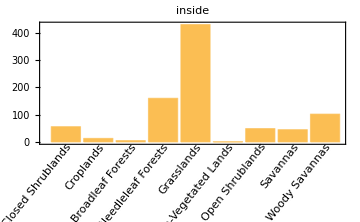
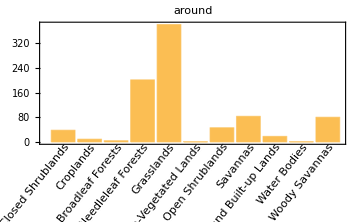
Dominant vegetation types by number of wildfires | 
-Graphics- | -Graphics-

```mathematica
Grid[{{Style["Dominant vegetation types by number of wildfires",18],SpanFromLeft},Function[i,BarChart[KeySort@Counts@DeleteMissing@Query[Values,#[i][[1]]&][dominantVegClassAssociationFiltered],ChartLabels->Placed[Automatic,{{0.5,0},{0.9,1}},Rotate[#,(2/7) Pi]&],Frame->True,PlotLabel->i,ImageSize->Medium]]/@{"inside","around"}}]
```

Dense Herbaceous vegetation class dominates both inside and around the forest, this is not surprising as this is the most abundant vegetation class in California. The second most abundant class is Evergreen Needleleaf Forests.

#### Vegetation bar plot inside and around burn areas when they are different

```mathematica
burnVegDiff=Query[Select[!StringMatchQ[#inside[[1]],#around[[1]]]&]][dominantVegClassAssociationFiltered];
```

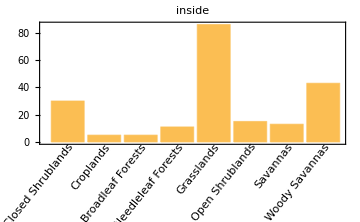
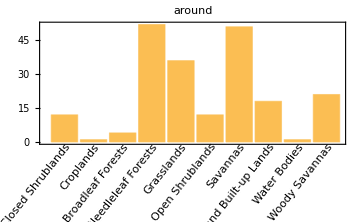
Dominant vegetation types when they are different inside and around each fire | 
-Graphics- | -Graphics-

```mathematica
Grid[{{Style["Dominant vegetation types when they are different inside and around each fire",18],SpanFromLeft},Function[i,BarChart[KeySort@Counts@DeleteMissing@Query[Values,#[i][[1]]&][burnVegDiff],ChartLabels->Placed[Automatic,{{0.5,0},{0.9,1}},Rotate[#,(2/7) Pi]&],Frame->True,PlotLabel->i,ImageSize->Medium]]/@{"inside","around"}}]
```

Even when the dominant vegetation  types inside and around fires are different, the Grasslands type still is the most abundant in terms of the number of fires (inside area) it dominates. However, the dominant types around fires are Evergreen Broadleaf Forests, Savannas, and grasslands.

#### Create an array of vegetation probability within and around each fire

The idea here is to create an array of vegetation classes for each fire such that each element of the array is a percentage of all pixels inside the burn area. A background association “vegClassBackground” is created to get the same array size for each fire such that we will get a matrix in the end.

```mathematica
vegClassBackground=KeySort[Association[(#->0)&/@Values@vegClass]]
```

<|Closed Shrublands→0,Cropland/Natural Vegetation Mosaics→0,Croplands→0,Deciduous Broadleaf Forests→0,Evergreen Broadleaf Forests→0,Evergreen Needleleaf Forests→0,Grasslands→0,Mixed Forests→0,Non-Vegetated Lands→0,Open Shrublands→0,Permanent Wetlands→0,Savannas→0,Unclassified→0,Urban and Built-up Lands→0,Water Bodies→0,Woody Savannas→0|>

```mathematica
(*vegMatrixInside=With[{temp=KeySort[Merge[{getVegList[vegClass,burnAreaVegClass[Lookup[#,"Geometry"],targetRange,lcImageProj[Lookup[#,"IgDate"]["Year"]],10],"inside"],vegClassBackground},Total]]},
Values[N[temp/Total[temp]]]]&/@Normal@dsCaPoly;*)
```

```mathematica
(*vegMatrixAround=With[{temp=KeySort[Merge[{getVegList[vegClass,burnAreaVegClass[Lookup[#,"Geometry"],targetRange,lcImageProj[Lookup[#,"IgDate"]["Year"]],10],"around"],vegClassBackground},Total]]},
Values[N[temp/Total[temp]]]]&/@Normal@dsCaPoly;*)
```

```mathematica
{vegMatrixInside,vegMatrixAround}=Import[NotebookDirectory[]<>"vegMatricesType2.wxf"];
```

#### In case matrices were just computed, save as WXF file

```mathematica
(*BinaryWrite[NotebookDirectory[]<>"vegMatricesType2.wxf",ExportByteArray[{vegMatrixInside,vegMatrixAround},"WXF"]];*)
```

```mathematica
(*Close[NotebookDirectory[]<>"vegMatricesType2.wxf"];*)
```

## Machine Learning methods: vegetation classification

The goal is to create a classifier to predict whether a given vegetation list is inside or around a fire. For the first try, only have vegetation data plugged in in the form of a matrix according to vegMatrixInside and vegMatrixOutside

#### Remove any arrays that have any “unclassified” pixels and drop any element because array elements sum to 1 without loss of information

```mathematica
unclassifiedPos=First@First@Position[Keys[vegClassBackground],"Unclassified"]
```

13

```mathematica
vegMatrixInsideReduced=Drop[Select[vegMatrixInside,#[[unclassifiedPos]]==0&],None,{1}];
```

```mathematica
vegMatrixAroundReduced=Drop[Select[vegMatrixAround,#[[unclassifiedPos]]==0&],None,{1}];
```

#### Join matrices by threading a Rule between each array and “inside” or “around”

```mathematica
vegMatrixAll=Join[Thread[vegMatrixInsideReduced->"inside"],Thread[vegMatrixAroundReduced->"around"]];
```

#### Do a 70-30 split for training and validation

```mathematica
testVegMat=RandomSample[vegMatrixAll,Round[Length[vegMatrixAll]*0.3]];trainingVegMat=Complement[vegMatrixAll,testVegMat];
```

#### Train a classifier

```mathematica
insideOrAround=Classify[trainingVegMat,PerformanceGoal->"Quality",ValidationSet->testVegMat]
```

ClassifierFunction[…]

#### Evaluate performance

```mathematica
Information[insideOrAround]
```

Classifier information
Data type | NumericalVector (length: 15)
Classes | ,,aroundinside
Accuracy | (61.82.2) %
Method | RandomForest
Single evaluation time | 8.99 ms/example
Batch evaluation speed | 8.4 examples/ms
Loss | 0.677 ± 0.0046
Model memory | 614. kB
Training examples used | 1107 examples
Training time | 3.94 s
 |

From the information above, the accuracy of the classifier was ~63% which is a bit higher than the baseline accuracy of 50%. The baseline accuracy is 50% because the dataset is balanced which means that there are as many arrays for inside and for around the fire.

```mathematica
ClassifierMeasurements[insideOrAround,testVegMat,"AreaUnderROCCurve"]
```

<|around→0.691774,inside→0.693697|>

The Area under the ROC is about 70% which is not bad but not too good.

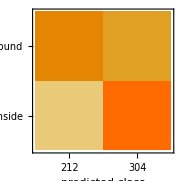

```mathematica
ClassifierMeasurements[insideOrAround,testVegMat,"ConfusionMatrixPlot"]
```

A large number is misclassified.

Future work: Do a scalewise variation. Pick incrementally larger study areas. (Tirtha) Split vegetation into coastal and inland to evaluate fuel-driven vs wind-driven fires. Drop fires that have water bodies and barren lands around them to see if classifier still gets 63% accuracy. We suspect the relatively high accuracy might be an artefact of that.

#### Trying an an unsupervised method, DimensionReduce, to see if there is a clear split

```mathematica
features=DimensionReduce[Join[vegMatrixInsideReduced,vegMatrixAroundReduced],Method->"TSNE"];
```

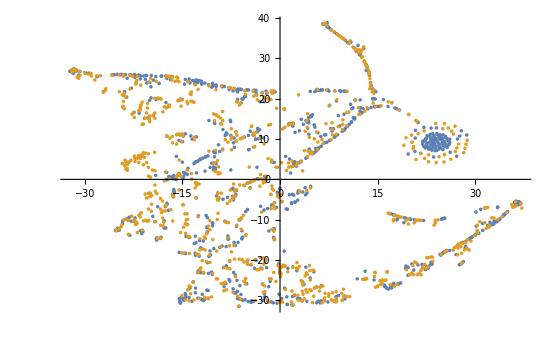

```mathematica
ListPlot[With[{len=features//Length},{features[[;;Round[len/2]]],features[[Round[len/2]+1;;]]}]]
```

There is no clear split but Stephen thinks there might be something behind this structure and that it is worth studying more deeply.

## Machine Learning methods: vegetation and elevation combined

### Visualization and computation

#### Visualize elevation raster for the WOOLSEY fire of 2018

```mathematica
viz[burnAreaRasIm[dsCaPoly[21,"Geometry"],targetRange,elevImProj]]
```

#### Compute mean and std of elevation and slope of each fire

```mathematica
(*burnRasImElevList=ResourceFunction["DynamicMap"][burnAreaRasIm[dsCaPoly[#,"Geometry"],targetRange,elevImProj]&,Range[Length[dsCaPoly]]];*)
```

```mathematica
(*meanStdElevList=ResourceFunction["DynamicMap"][(Through[{Mean,StandardDeviation}[PixelValue[#2,#1,"Bit16"]]]&)@@burnRasImList[[#]]&,Range[Length[dsCaPoly]]];*)
```

```mathematica
(*meanStdElevAroundList=ResourceFunction["DynamicMap"][(Through[{Mean,StandardDeviation}[PixelValue[#2,Dilation[#1,DiskMatrix[5]]-#1,"Bit16"]]]&)@@burnRasImList[[#]]&,Range[Length[dsCaPoly]]];*)
```

```mathematica
(*meanStdSlopeList=ResourceFunction["DynamicMap"][(Through[{Mean,StandardDeviation}[PixelValue[GradientFilter[#2,1],Dilation[#1,DiskMatrix[5]]-#1,"Real64"]]]&)@@burnRasImList[[#]]&,Range[Length[dsCaPoly]]];*)
```

```mathematica
{burnRasImElevList,meanStdElevList,meanStdElevAroundList,meanStdSlopeList}=Import[NotebookDirectory[]<>"elevStats.wxf"];
```

#### In case meanElevList was just computed, save as WXF file

```mathematica
(*BinaryWrite[NotebookDirectory[]<>"elevStats.wxf",ExportByteArray[{burnRasImElevList,meanStdElevList,meanStdElevAroundList,meanStdSlopeList},"WXF"]];*)
```

```mathematica
(*Close[NotebookDirectory[]<>"elevStats.wxf"];*)
```

### Elevation statistics for California wildfires

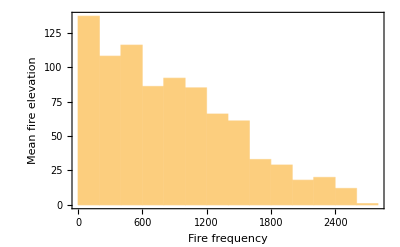

```mathematica
Histogram[meanStdElevAroundList[[All,1]],Frame->True,FrameLabel->{{"Mean fire elevation",None},{"Fire frequency","Histogram of mean fire elevations"}}]
```

### Classifier to predict whether a given vegetation list is inside or around a fire including mean fire elevation data as well as vegetation

#### Define whitening transformation

This is to drop the infinite precision assumption and make computations faster.

```mathematica
whiteningTransformation[list_]:=With[{listFast=list*1.0},Transpose@((Transpose@listFast-Mean[listFast])/StandardDeviation[listFast])];
```

#### Remove any arrays that have any “unclassified” pixels and drop any element because array elements sum to 1 without loss of information

```mathematica
vegElevMatrixInside=Drop[Select[Join[vegMatrixInside,Partition[whiteningTransformation[meanStdElevList[[All,1]]],1],2],#[[unclassifiedPos]]==0&],None,{1}];
```

```mathematica
vegElevMatrixAround=Drop[Select[Join[vegMatrixAround,Partition[whiteningTransformation[meanStdElevAroundList[[All,1]]],1],2],#[[unclassifiedPos]]==0&],None,{1}];
```

#### Combine matrices and thread rules

```mathematica
vegElevMatrixAll=Join[Thread[vegElevMatrixInside->"inside"],Thread[vegElevMatrixAround->"around"]];
```

#### Split into training and validation 70-30

```mathematica
testVegElevMat=RandomSample[vegElevMatrixAll,Round[Length[vegElevMatrixAll]*0.3]];trainingVegElevMat=Complement[vegElevMatrixAll,testVegElevMat];
```

#### Train classifier

```mathematica
insideOrAroundElev=Classify[trainingVegElevMat,PerformanceGoal->"Quality",ValidationSet->testVegElevMat]
```

ClassifierFunction[…]

```mathematica
Information[insideOrAroundElev]
```

Classifier information
Data type | NumericalVector (length: 16)
Classes | ,,aroundinside
Accuracy | (65.53.0) %
Method | GradientBoostedTrees
Single evaluation time | 7.11 ms/example
Batch evaluation speed | 10.9 examples/ms
Loss | 0.65 ± 0.031
Model memory | 404. kB
Training examples used | 1181 examples
Training time | 3.46 s
 |

Accuracy has improved by 4%

```mathematica
ClassifierMeasurements[insideOrAroundElev,testVegElevMat,"AreaUnderROCCurve"]
```

<|around→0.738152,inside→0.738333|>

AUC has increased by 5%

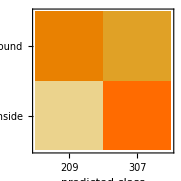

```mathematica
ClassifierMeasurements[insideOrAroundElev,testVegElevMat,"ConfusionMatrixPlot"]
```

### Classifier that includes mean fire slope

#### Compute matrices with the same dropping of “unclassified” cases

```mathematica
vegSlopeMatrixInside=Drop[Select[Join[vegMatrixInside,Partition[whiteningTransformation[meanStdSlopeList[[All,1]]],1],2],#[[unclassifiedPos]]==0&],None,{1}];
```

```mathematica
vegSlopeMatrixAround=Drop[Select[Join[vegMatrixAround,Partition[whiteningTransformation[meanStdSlopeList[[All,1]]],1],2],#[[unclassifiedPos]]==0&],None,{1}];
```

#### Combine matrices

```mathematica
vegSlopeMatrixAll=Join[Thread[vegSlopeMatrixInside->"inside"],Thread[vegSlopeMatrixAround->"around"]];
```

#### Training and testing data

```mathematica
testVegSlopeMat=RandomSample[vegSlopeMatrixAll,Round[Length[vegSlopeMatrixAll]*0.3]];trainingVegSlopeMat=Complement[vegSlopeMatrixAll,testVegSlopeMat];
```

#### Train classifier

```mathematica
insideOrAroundSlope=Classify[trainingVegSlopeMat,PerformanceGoal->"Quality",Method->"GradientBoostedTrees"]
```

ClassifierFunction[…]

#### Classifier information

```mathematica
Information[insideOrAroundSlope]
```

Classifier information
Data type | NumericalVector (length: 16)
Classes | ,,aroundinside
Accuracy | (64.4.) %
Method | GradientBoostedTrees
Single evaluation time | 11. ms/example
Batch evaluation speed | 13.6 examples/ms
Loss | 0.668 ± 0.031
Model memory | 438. kB
Training examples used | 1196 examples
Training time | 3.81 s
 |

```mathematica
ClassifierMeasurements[insideOrAroundSlope,testVegSlopeMat,"AreaUnderROCCurve"]
```

<|around→0.730713,inside→0.730773|>

Classifier with mean elevation seems to fare better when it comes to AUC.

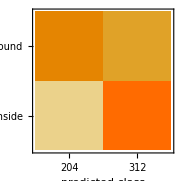

```mathematica
ClassifierMeasurements[insideOrAroundSlope,testVegSlopeMat,"ConfusionMatrixPlot"]
```

Future work: Include only slopes around the fire and differentiate whether they are going into or out of the fires.

## Future work: testing the wind-driven vs fuel-driven fire paradigms

Recently, California fires were categorized as either wind-driven or fuel driven (Keeley & Syphard, 2019). Typically in the mid- and north-western parts of the state, fuel-driven fires occur in regions where fire suppression and silvicultural practices have led to the accumulation of fuels where, historically, many fires occurred. Fuel-driven fires are usually caused by lightning and occur in the summer months (July & August). In contrast, wind-driven fires occur on the eastern part of the state. In the autumn, a high pressure system in the interior basin and a low pressure system over the Pacific means that high-speed offshore winds develop. These winds tend to intensify small fires, typically caused by humans, to form large conflagrations.

Examples of fuel driven fires are the Rush (2012), Rim (2013), Rough (2015), and Marble Cone (2007) fires

Examples of wind-driven fires are the Thomas (2017), Witch (2007), Camp (2018) fires

```mathematica
dsCa[;;60,{"IncidName","IgDate"}]
```

```mathematica
dsCa[2]
```

```mathematica
vegClass=Rule@@@Thread[{lcPropVals,{"Water Bodies","Evergreen Needleleaf Forests","Evergreen Broadleaf Forests","Deciduous Broadleaf Forests","Mixed Forests","Closed Shrublands","Open Shrublands","Woody Savannas","Savannas","Grasslands","Permanent Wetlands","Croplands","Urban and Built-up Lands","Cropland/Natural Vegetation Mosaics","Non-Vegetated Lands","Unclassified"}}]
```

{0→Water Bodies,1→Evergreen Needleleaf Forests,2→Evergreen Broadleaf Forests,4→Deciduous Broadleaf Forests,5→Mixed Forests,6→Closed Shrublands,7→Open Shrublands,8→Woody Savannas,9→Savannas,10→Grasslands,11→Permanent Wetlands,12→Croplands,13→Urban and Built-up Lands,14→Cropland/Natural Vegetation Mosaics,15→Non-Vegetated Lands,255→Unclassified}

```mathematica
colRule=Rule@@@Thread[{lcPropVals,Join[{Black},Take[ColorData[54,"ColorList"],Length[lcPropVals]-2],{LightBlue}]}]
```

{0→GrayLevel[0],1→RGBColor[0.782803, 0.164904, 0.400458],2→RGBColor[0.909499, 0.613916, 0.204196],4→RGBColor[0.806577, 0.385397, 0.762768],5→RGBColor[0.698817, 0.873304, 0.295247],6→RGBColor[0.378897, 0.873304, 0.787549],7→RGBColor[1, 0.529198, 0.324819],8→RGBColor[1, 0.998367, 0.434775],9→RGBColor[0.873304, 0.150484, 0.255131],10→RGBColor[0.723598, 0.791043, 0.963806],11→RGBColor[0.85037, 0.558389, 0],12→RGBColor[1, 0.998856, 0.00207523],13→RGBColor[0.273106, 0.542992, 0.495583],14→RGBColor[1, 0.740871, 0.828473],15→RGBColor[0.630091, 0.148196, 0.579461],255→RGBColor[0.87, 0.94, 1]}

```mathematica
viz[burnAreaRasIm[dsCaPoly[8,"Geometry"],targetRange,lcImageProj[2008],10],colRule]
```

How do you account for firelines created by fire fighters? Only The Brave movie.

## Future work: weather data

Use WeatherData. DayMet by ORNL. Daily meteorological values at surface based on observations. Temp (min and max; better for heat stress; deviation from climatic average; pentads: multiples of 5 days), Rainfall (last time, and cumulative).

Lauren: LandSurface index gives an idea of vegetation stress -> probability for my vegetation to burn. What type of soil do you have? If you have a lot of organic matter, then it plays a big role. SOM (Soil Organic Matter). if SOM % datasets don’t exist a lot, knowing soil porosity would be a good substitute.

Morphological components and see how many regions are covered to see how many roads the fire

Weather radar and precipitation.

```mathematica
dsCa[1,{"BurnBndLat","BurnBndLon","IgDate"}]
```

```mathematica
Normal@Values@dsCa[1,{"BurnBndLat","BurnBndLon"}]
```

{39.269,-122.775}

```mathematica
dsCa[5,"IgDate"]+LinguisticAssistant
```

Mon 19 Aug 2013

```mathematica
AirTemperatureData[ToExpression@Normal@Values@dsCa[5,{"BurnBndLat","BurnBndLon"}],{dsCa[5,"IgDate"],dsCa[5,"IgDate"]+Quantity[1, "Days"]}]
```

TimeSeries[…]

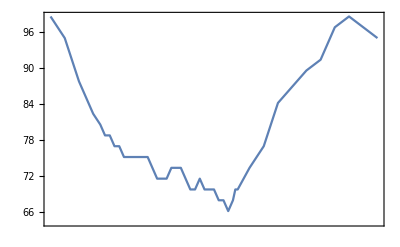

```mathematica
DateListPlot[%]
```

```mathematica
AirTemperatureData[ToExpression@Normal@Values@dsCa[5,{"BurnBndLat","BurnBndLon"}],{dsCa[5,"IgDate"]-Quantity[5, "Days"],dsCa[5,"IgDate"]+Quantity[5, "Days"],"Day"}]
```

TimeSeries[…]

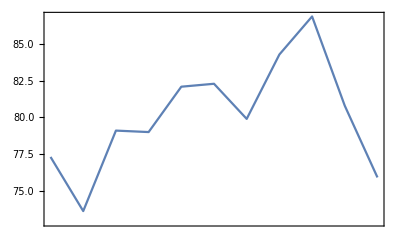

```mathematica
DateListPlot[%]
```

```mathematica
WindSpeedData[ToExpression@Normal@Values@dsCa[5,{"BurnBndLat","BurnBndLon"}],{dsCa[5,"IgDate"]-Quantity[5, "Days"],dsCa[5,"IgDate"]+Quantity[5, "Days"],"Day"}]
```

TimeSeries[…]

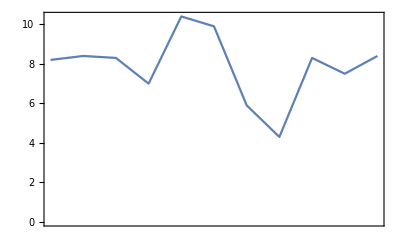

```mathematica
DateListPlot[%]
```

```mathematica
WindSpeedData[ToExpression@Normal@Values@dsCa[5,{"BurnBndLat","BurnBndLon"}],{dsCa[5,"IgDate"]-Quantity[5, "Days"],dsCa[5,"IgDate"]+Quantity[5, "Days"],"Day"}]
```

```mathematica
WeatherData[ToExpression@Normal@Values@dsCa[2,{"BurnBndLat","BurnBndLon"}],"Temperature",dsCa[2,"IgDate"],TimeZone->"America/Los_Angeles"]
```

TimeSeries[…]

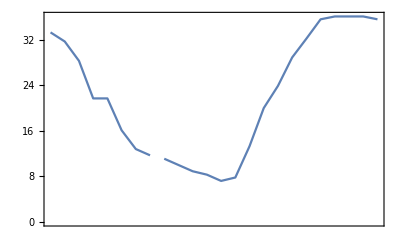

```mathematica
DateListPlot[%]
```

```mathematica
$TimeZone
```

-4.

```mathematica
WeatherData["Chicago","Temperature",Yesterday]
```

TimeSeries[…]

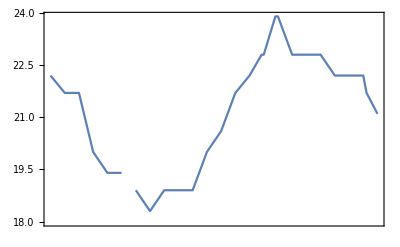

```mathematica
DateListPlot[%]
```